EJERCICIO 1

```mathematica
Limit[G[n],n-> ∞]
```

1

```mathematica
G[n_]:=((n+1)/(n-√n))^(√(n+2)-√n)
```

EJERICIO 2:

```mathematica
Limit[Log[n^5]/(√n),n->∞]
```

0

Log(n) <<Raiz (n)

EJERCICIO 3:

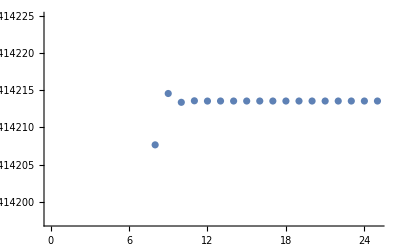

```mathematica
ListPlot[RecurrenceTable[{a[n+1]==2+1/a[n], a[1]==5},a[n],{n,1,25}]]
```

EJERCICIO 5:

```mathematica
Clear[a]
```

```mathematica
RSolve[{a[n]==3a[n-1]+n, a[1]==0}, a[n], n]
```

{{a[n]→1/12 (-9+5 3^n-6 n)}}

```mathematica
Limit[(1/12*(-9+5*3^n-6n))/3^n,n->Infinity]
```

5/12

EJERCICIO 6:

```mathematica
RSolve[{a[n]==a[n-1]+a[n-2],a[1]==2, a[2]==3}, a[n],n]
```

{{a[n]→1/2 (3 Fibonacci[n]+LucasL[n])}}